## Chapter 7 Problem 14: Density functional for helium atom

#### This notebook carries out the calculation in Section 7.6.5. Some parts of the problem are solved in the text of the solutions manual.

```mathematica
Remove["Global`*"]
$Assumptions={r>0};
```

#### b. Show that (7.104) is properly normalized

```mathematica
n0Test=(Zeff^3/(4 Pi))Exp[-Zeff r];
4Pi Integrate[r^2n0Test,{r,0,∞},Assumptions->Zeff>0]
```

2

#### c. Do the angular integral to get (7.105) and save it for later

```mathematica
invXXp=Integrate[1/Sqrt[rp^2-2r rp μ+r^2],
{μ,-1,1},Assumptions->r>0]
```

4/(√((r-rp)^2)+√((r+rp)^2))

#### d. Now do the work to obtain the first order Kohn-Sham wave function

Set the value of Z for the starting density, for the  basis functions, and for the external potential

```mathematica
Zn=2-5/16;
Zϕ=2-5/16;
Zx=2;
```

Define the function that is the starting approximation for the density, and check the normalization

```mathematica
n0[r_]=Zn^3 Exp[-Zn r]/(4 Pi);
4 Pi Integrate[r^2n0[r],{r,0,∞}]==2
```

True

Set up the radial l=0 wave functions, and check the normalizations.

```mathematica
Rnl[r_]=(2 Zϕ r/(n a0))^l Exp[-Zϕ r/(n a0)]Hypergeometric1F1[-n+l+1,2l+2,2Zϕ r/(n a0)];
Nnl=1/(2l+1)! Sqrt[(2Zϕ/n )^3(n+l)!/(2n(n-l-1)!)];
```

```mathematica
R10=Nnl Rnl[s]/.{n->1,l->0,s->r a0};
R20=Nnl Rnl[s]/.{n->2,l->0,s->r a0};
R30=Nnl Rnl[s]/.{n->3,l->0,s->r a0};
```

```mathematica
Integrate[r^2 R10^2,{r,0,∞}]==1
Integrate[r^2 R20^2,{r,0,∞}]==1
Integrate[r^2 R30^2,{r,0,∞}]==1
```

True

True

True

Define the function that is the external potential

```mathematica
vExt[r_]=-Zx/r;
```

Get the exchange correlation contribution to the KS potential. Follow J.Chem.Phys. 144(2016)191101

```mathematica
hx0=1.174;
ϵX[n_]=hx0(-3/(4Pi)(3 Pi^2 n)^(1/3));
vX[n_]=D[n ϵX[n],n];
```

```mathematica
rs=(4 Pi n/3)^(-1.0/3.0);
ϵC[n_]=-0.0233504/(1+0.1018+0.0233504 Sqrt[rs]+0.102582 rs);
vC[n_]=D[n ϵC[n],n];
```

```mathematica
ϵXC[n_]=ϵX[n]+ϵC[n];
vXC[n_]=vX[n]+vC[n];
vXC0=vXC[n0[r]];
```

Find the matrix elements in this basis for the Kohn-Sham Hamiltonian. Do it all numerically, with some reasonable precision.

```mathematica
wkpcsn=15;
basis={R10,R20,R30};
right1=-(1/2)(1/r^2)D[r^2 D[basis,r],r]+(vExt[r]+vXC0 )basis;
intgd1=Outer[Times,basis,right1];
right2=2Pi rp^2n0[rp]invXXp basis;
intgd2=Outer[Times,basis,right2];
hKS=NIntegrate[r^2 intgd1,{r,0,∞},WorkingPrecision->wkpcsn]+
NIntegrate[r^2 intgd2,{r,0,∞},{rp,0,∞},WorkingPrecision->wkpcsn];
```

```mathematica
MatrixForm[hKS]
```

(-1.1236329986418 | -0.054249286340506 | -0.031468902065064
-0.054249286340153 | -0.02397911124979 | 0.034998262091523
-0.031468902066107 | 0.034998261800538 | 0.05313954502786)

Diagonalize and get the ground state eigenvalue and  wave function; Check normalization

```mathematica
eigs=Eigensystem[hKS]
```

{{-1.127051508506,0.06868431154075,-0.03610536789844},{{-0.9985147532487,-0.04830782976316,-0.02519208463702},{-0.04147630815636,0.3741859400192,0.9264257110819},{0.03532709179489,-0.9260946160064,0.3756338094331}}}

```mathematica
gsEnrg1=eigs[[1]][[1]]
gsCoef1=eigs[[2]][[1]]
```

-1.127051508506

{-0.9985147532487,-0.04830782976316,-0.02519208463702}

The above values (times -1) are the coefficients in (7.108)

```mathematica
ϕ01=gsCoef1[[1]]R10+gsCoef1[[2]]R20+gsCoef1[[3]]R30;
Integrate[r^2 ϕ01^2,{r,0,∞}]==1
```

True

#### e. Complete the calculation and reproduce Table 7.1 and Figure 7.7

Calculate the next iteration of the density and check normalization.

```mathematica
n1[r_]=2ϕ01^2/(4 Pi);
4 Pi Integrate[r^2n1[r],{r,0,∞}]==2
```

True

Calculate the energy functional. For TKS, don’t forget the 1/Sqrt[2Pi] in the wave function.

```mathematica
wkpcsn=12;
funcVext1=4 Pi NIntegrate[r^2 vExt[r] n1[r],{r,0,∞},WorkingPrecision->wkpcsn];
funcTKS1=2  NIntegrate[r^2 ϕ01 (-(1/2)(1/r^2)D[r^2 D[ϕ01,r],r]),{r,0,∞},WorkingPrecision->wkpcsn];
funcUee1=(1/2)NIntegrate[4 Pi r^2 n1[r]2Pi rp^2n1[rp]invXXp,
{r,0,∞},{rp,0,∞},WorkingPrecision->wkpcsn];
funcUxc1=4Pi NIntegrate[r^2n1[r]ϵXC[n1[r]],{r,0,∞},WorkingPrecision->wkpcsn];
funcE1=funcVext1+funcTKS1+funcUee1+funcUxc1;
```

Get the value of a “Hartree” in eV (by going through SI)

```mathematica
e=QuantityMagnitude[UnitConvert[Quantity["ElementaryCharge"]]];
hartree=2QuantityMagnitude[UnitConvert[Quantity["Rydbergs"]]]/e
```

27.211386246

Put in dimensions and compare to experimental value -78.8 eV

```mathematica
funcE1  hartree
```

-78.264914814

Now do it again for the second iteration.

```mathematica
vXC1=vXC[n1[r]];
```

```mathematica
wkpcsn=10;
right1=-(1/2)(1/r^2)D[r^2 D[basis,r],r]+(vExt[r]+vXC1 )basis;
intgd1=Outer[Times,basis,right1];
right2=2Pi rp^2n1[rp]invXXp basis;
intgd2=Outer[Times,basis,right2];
hKS=NIntegrate[r^2 intgd1,{r,0,∞},WorkingPrecision->wkpcsn]+
NIntegrate[r^2 intgd2,{r,0,∞},{rp,0,∞},WorkingPrecision->wkpcsn];
```

```mathematica
MatrixForm[hKS]
```

(-0.541442084 | 0.050624382 | 0.02130269
0.05062438 | 0.12322437 | 0.0862863319
0.021306113 | 0.0862619592 | 0.08828021)

```mathematica
eigs=Eigensystem[hKS]
```

{{-0.54562429,0.1975395,0.01814728},{{-0.99709382,0.072416727,0.023658745},{0.07122856,0.77607087,0.62661033},{-0.027033528,-0.62657795,0.77888976}}}

```mathematica
gsEnrg2=eigs[[1]][[1]]
gsCoef2=eigs[[2]][[1]]
```

-0.54562429

{-0.99709382,0.072416727,0.023658745}

```mathematica
Total[gsCoef2^2]
```

1.

```mathematica
ϕ02=gsCoef2[[1]]R10+gsCoef2[[2]]R20+gsCoef2[[3]]R30;
Integrate[r^2 ϕ02^2,{r,0,∞}]==1
```

True

```mathematica
n2[r_]=2ϕ02^2/(4 Pi);
```

```mathematica
wkpcsn=9;
funcVext2=4 Pi NIntegrate[r^2 vExt[r] n2[r],{r,0,∞},WorkingPrecision->wkpcsn];
funcTKS2=2  NIntegrate[r^2 ϕ02(-(1/2)(1/r^2)D[r^2 D[ϕ02,r],r]),{r,0,∞},WorkingPrecision->wkpcsn];
funcUee2=(1/2)NIntegrate[4 Pi r^2 n2[r]2Pi rp^2n2[rp]invXXp,
{r,0,∞},{rp,0,∞},WorkingPrecision->wkpcsn];
funcUxc2=4Pi NIntegrate[r^2n2[r]ϵXC[n2[r]],{r,0,∞},WorkingPrecision->wkpcsn];
funcE2=funcVext2+funcTKS2+funcUee2+funcUxc2;
```

One more iteration

```mathematica
vXC2=vXC[n2[r]];
```

```mathematica
wkpcsn=9;
right1=-(1/2)(1/r^2)D[r^2 D[basis,r],r]+(vExt[r]+vXC2)basis;
intgd1=Outer[Times,basis,right1];
right2=2Pi rp^2n2[rp]invXXp basis;
intgd2=Outer[Times,basis,right2];
hKS=NIntegrate[r^2 intgd1,{r,0,∞},WorkingPrecision->wkpcsn]+
NIntegrate[r^2 intgd2,{r,0,∞},{rp,0,∞},WorkingPrecision->wkpcsn];
```

```mathematica
eigs=Eigensystem[hKS];
gsEnrg3=eigs[[1]][[1]];
gsCoef3=eigs[[2]][[1]];
ϕ03=gsCoef3[[1]]R10+gsCoef3[[2]]R20+gsCoef3[[3]]R30;
```

```mathematica
n3[r_]=2ϕ03^2/(4 Pi);
```

```mathematica
wkpcsn=8;
funcVext3=4 Pi NIntegrate[r^2 vExt[r] n3[r],{r,0,∞},WorkingPrecision->wkpcsn];
funcTKS3=2  NIntegrate[r^2 ϕ03(-(1/2)(1/r^2)D[r^2 D[ϕ03,r],r]),{r,0,∞},WorkingPrecision->wkpcsn];
funcUee3=(1/2)NIntegrate[4 Pi r^2 n3[r]2Pi rp^2n3[rp]invXXp,
{r,0,∞},{rp,0,∞},WorkingPrecision->wkpcsn];
funcUxc3=4Pi NIntegrate[r^2n3[r]ϵXC[n3[r]],{r,0,∞},WorkingPrecision->wkpcsn];
funcE3=funcVext3+funcTKS3+funcUee3+funcUxc3;
```

Plot the densities

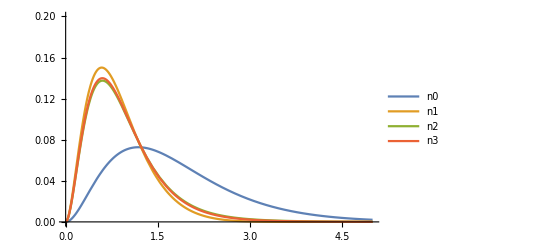

```mathematica
Plot[{r^2n0[r],r^2n1[r],r^2n2[r],r^2n3[r]},{r,0,5},PlotRange->{0,0.2},PlotLegends->{n0,n1,n2,n3}]
```

Tabulate the energies

```mathematica
energies={
{1,funcVext1,funcTKS1,funcUee1,funcUxc1,hartree funcE1},
{2,funcVext2,funcTKS2,funcUee2,funcUxc2,hartree funcE2},
{3,funcVext3,funcTKS3,funcUee3,funcUxc3,hartree funcE3}};
N[Grid[energies]]
```

1. | -6.90876 | 2.9882 | 2.17546 | -1.13109 | -78.2649
2. | -6.48303 | 2.63504 | 1.99548 | -1.04472 | -78.8379
3. | -6.56468 | 2.6978 | 2.03054 | -1.06127 | -78.8478